# Shadow Drawings

--Jason, August 2015. 

This is a notebook to parse files in the form <n>diagrams.txt produced by the drawpd.py script and produce nice, adjustable drawings of the shadows. (Drawings of actual diagrams are more difficult, because we have to break the lines at crossings.)

```mathematica
IsHashQ[str_] := And[StringLength[str] == 31,Not[StringMatchQ[str,__~~"-->"~~__]]];
```

We have a kind of interesting Mathematica programming problem in the middle. We have a list of lists of 2-element lists giving (oriented) arrows. We want to assemble them into “runs” according to the rule {a,...,k},{k,..z} -> {a,...,z}, and stop when we get to the form {a,....,a}. Let’s do some experiments:

```mathematica
CanLinkQ[a_,b_] := Last[a] == First[b];
OneRound[L_] := Module[{complete,incomplete,match},complete = Select[L,Last[#]==First[#]&];
If [Length[complete] == Length[L],
complete,
incomplete = Complement[L,complete];
match =Select[incomplete[[2;;]],CanLinkQ[incomplete[[1]],#]&];
Join[complete,{Join[incomplete[[1]],match[[1,2;;]]]},Complement[incomplete[[2;;]],match]]
]
];
```

```mathematica
Nest[OneRound,{{1,2},{2,3},{3,4},{4,5},{5,1},{23,24,25,26,27,23}},5]
```

{{23,24,25,26,27,23},{3,4,5,1,2,3}}

```mathematica
ReadDiagrams[n_] := Module[{txtfile,words,hashpositions,rawshads},
txtfile = Import["/Users/cantarel/randomdiagram/data/csdrawings/" <> ToString[n]<>"vertices.txt"];
words = ReadList[StringToStream[txtfile],Word];
hashpositions = Flatten[Position[words,_?IsHashQ,{1},Heads->False]];
rawshads = words[[#[[1]]+2;;#[[2]]-1]]&/@Partition[hashpositions,2,1];ToExpression[FixedPoint[OneRound,#]&/@ (Flatten[#,1]& /@Map[StringCases[#,"("~~x1__~~","~~y1__~~")-->("~~x2__~~","~~y2__~~")"->{{ToExpression[x1],ToExpression[y1]},{ToExpression[x2],ToExpression[y2]}}] & ,rawshads,{2}])]
];
```

```mathematica
testpoints =  ReadDiagrams[3][[1]]
```

{{{323.333,470.},{176.667,470.},{176.667,176.667},{470.,176.667},{470.,323.333},{30.,323.333},{30.,30.},{323.333,30.},{323.333,470.}}}

```mathematica
MakeGraphic[L_] := Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon @@L}];
```

We can now export the various .pdf files for inclusion in the TEX document. It’s probably better to organize them into grids from Mathematica rather than do it on the page, since that will require a lot of weird TEX hackery in the paper file.

```mathematica
KnotGraphics[n_] := MakeGraphic /@ ReadDiagrams[n];
```

```mathematica
allgraphics= Join[KnotGraphics[3],KnotGraphics[4],KnotGraphics[5]];
```

We now give some code to make an “nxk” graphic of knot diagrams:

```mathematica
KnotGridFigure[across_,down_] := GraphicsGrid[Partition[allgraphics[[1;;across down]],across]];
```

```mathematica
Export["/Users/cantarel/plcurve/figs/knotgrid.pdf",KnotGridFigure[7,6]]
```

/Users/cantarel/plcurve/figs/knotgrid.pdf

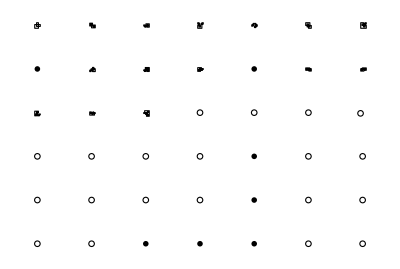

```mathematica
KnotGridFigure[7,6]
```